## Data opening

```mathematica
Vibrio=Import[NotebookDirectory[]<>"Vibrio.csv"];
Ecoli=Import[NotebookDirectory[]<>"Ecoli.csv"];
Alginate=Import[NotebookDirectory[]<>"Alginate.csv"];
CSAlginate=Import[NotebookDirectory[]<>"CSalginate.csv"];
Acetate=Import[NotebookDirectory[]<>"Acetate.csv"];
HP=Import[NotebookDirectory[]<>"3HP.csv"];
```

```mathematica
Acetatedata=Table[{Acetate[[i,1]],(Acetate[[i,2]]+Acetate[[i,3]])/2},{i,2,Length[Acetate]}];
Acetatedata05=Table[{Acetate[[i,1]],(Acetate[[i,4]]+Acetate[[i,5]])/2},{i,2,Length[Acetate]}];
Acetatedata10=Table[{Acetate[[i,1]],(Acetate[[i,6]]+Acetate[[i,7]])/2},{i,2,Length[Acetate]}];
Acetatedata20=Table[{Acetate[[i,1]],(Acetate[[i,8]]+Acetate[[i,9]])/2},{i,2,Length[Acetate]}];
```

```mathematica
HPdata=Table[{HP[[i,1]],(HP[[i,2]]+HP[[i,3]])/2},{i,2,Length[HP]}];
HPdata05=Table[{HP[[i,1]],(HP[[i,4]]+HP[[i,5]])/2},{i,2,Length[HP]}];
HPdata10=Table[{HP[[i,1]],(HP[[i,6]]+HP[[i,7]])/2},{i,2,Length[HP]}];
HPdata20=Table[{HP[[i,1]],(HP[[i,8]]+HP[[i,9]])/2},{i,2,Length[HP]}];
```

```mathematica
HPinter=Interpolation[HPdata,InterpolationOrder->1,Method->"Spline"];
HPinter05=Interpolation[HPdata05,InterpolationOrder->1,Method->"Spline"];
HPinter10=Interpolation[HPdata10,InterpolationOrder->1,Method->"Spline"];
HPinter20=Interpolation[HPdata20,InterpolationOrder->1,Method->"Spline"];
```

```mathematica
Vibriodata=Table[{Vibrio[[i,1]],(Vibrio[[i,2]]+Vibrio[[i,3]])/2},{i,2,Length[Vibrio]}];
Vibriodata05=Table[{Vibrio[[i,1]],(Vibrio[[i,4]]+Vibrio[[i,5]])/2},{i,2,Length[Vibrio]}];
Vibriodata10=Table[{Vibrio[[i,1]],(Vibrio[[i,6]]+Vibrio[[i,7]])/2},{i,2,Length[Vibrio]}];
Vibriodata20=Table[{Vibrio[[i,1]],(Vibrio[[i,8]]+Vibrio[[i,9]])/2},{i,2,Length[Vibrio]}];
```

```mathematica
Vibinter=Interpolation[Table[{Vibrio[[i,1]],(Vibrio[[i,2]]+Vibrio[[i,3]])/2},{i,2,Length[Vibrio]}],InterpolationOrder->1];
Vibinter05=Interpolation[Table[{Vibrio[[i,1]],(Vibrio[[i,4]]+Vibrio[[i,5]])/2},{i,2,Length[Vibrio]}],InterpolationOrder->1];
Vibinter10=Interpolation[Table[{Vibrio[[i,1]],(Vibrio[[i,6]]+Vibrio[[i,7]])/2},{i,2,Length[Vibrio]}],InterpolationOrder->1];
Vibinter20=Interpolation[Table[{Vibrio[[i,1]],(Vibrio[[i,8]]+Vibrio[[i,9]])/2},{i,2,Length[Vibrio]}],InterpolationOrder->1];
```

```mathematica
Ecolidata=Table[{Ecoli[[i,1]],(Ecoli[[i,2]]+Ecoli[[i,3]])/2},{i,2,Length[Ecoli]}];
Ecolidata05=Table[{Ecoli[[i,1]],(Ecoli[[i,4]]+Ecoli[[i,5]])/2},{i,2,Length[Ecoli]}];
Ecolidata10=Table[{Ecoli[[i,1]],(Ecoli[[i,6]]+Ecoli[[i,7]])/2},{i,2,Length[Ecoli]}];
Ecolidata20=Table[{Ecoli[[i,1]],(Ecoli[[i,8]]+Ecoli[[i,9]])/2},{i,2,Length[Ecoli]}];
```

```mathematica
Ecoliinter=Interpolation[Ecolidata,InterpolationOrder->3,InterpolationOrder->1];
Ecoliinter05=Interpolation[Ecolidata05,InterpolationOrder->1,InterpolationOrder->1];
Ecoliinter10=Interpolation[Ecolidata10,InterpolationOrder->1,InterpolationOrder->1];
Ecoliinter20=Interpolation[Ecolidata20,InterpolationOrder->1,InterpolationOrder->1];
```

```mathematica
Alginatedata=Table[{Alginate[[i,1]],(Alginate[[i,2]]+Alginate[[i,3]])/2},{i,2,Length[Alginate]}];
Alginatedata05=Table[{Alginate[[i,1]],(Alginate[[i,4]]+Alginate[[i,5]])/2},{i,2,Length[Alginate]}];
Alginatedata10=Table[{Alginate[[i,1]],(Alginate[[i,6]]+Alginate[[i,7]])/2},{i,2,Length[Alginate]}];
Alginatedata20=Table[{Alginate[[i,1]],(Alginate[[i,8]]+Alginate[[i,9]])/2},{i,2,Length[Alginate]}];
Alginateinter=Interpolation[Alginatedata,InterpolationOrder->1];
Alginateinter05=Interpolation[Alginatedata05,InterpolationOrder->1];
Alginateinter10=Interpolation[Alginatedata10,InterpolationOrder->1];
Alginateinter20=Interpolation[Alginatedata20,InterpolationOrder->1];
```

```mathematica
CSAlginatedata=Table[{CSAlginate[[i,1]],(CSAlginate[[i,2]]+CSAlginate[[i,3]])/2},{i,2,Length[CSAlginate]}];
CSAlginatedata05=Table[{CSAlginate[[i,1]],(CSAlginate[[i,4]]+CSAlginate[[i,5]])/2},{i,2,Length[CSAlginate]}];
CSAlginatedata10=Table[{CSAlginate[[i,1]],(CSAlginate[[i,6]]+CSAlginate[[i,7]])/2},{i,2,Length[CSAlginate]}];
CSAlginatedata20=Table[{CSAlginate[[i,1]],(CSAlginate[[i,8]]+CSAlginate[[i,9]])/2},{i,2,Length[CSAlginate]}];
```

```mathematica
Acetateinter=Interpolation[Acetatedata,Method->"Spline"];
Acetateinter05=Interpolation[Acetatedata05,Method->"Spline"];
Acetateinter10=Interpolation[Acetatedata10,Method->"Spline"];
Acetateinter20=Interpolation[Acetatedata20,Method->"Spline"];
```

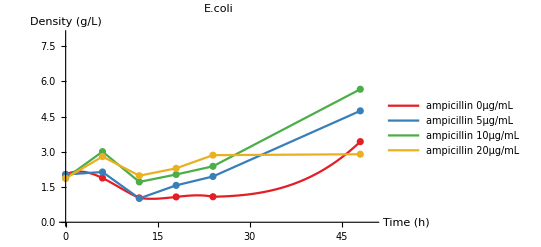

```mathematica
Show[Plot[{Ecoliinter[t],Ecoliinter05[t],Ecoliinter10[t],Ecoliinter20[t]},{t,0,48},PlotRange->{{0,50},{0,8}},PlotLegends->{"ampicillin 0μg/mL","ampicillin 5μg/mL","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["E.coli",Italic,Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{Ecolidata,Ecolidata05,Ecolidata10,Ecolidata20},PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```

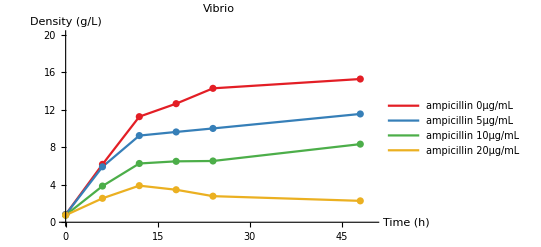

```mathematica
Show[Plot[{Vibinter[t],Vibinter05[t],Vibinter10[t],Vibinter20[t]},{t,0,48},PlotRange->{{0,50},{0,20}},PlotLegends->{"ampicillin 0μg/mL","ampicillin 5μg/mL","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["Vibrio",Italic,Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{Vibriodata,Vibriodata05,Vibriodata10,Vibriodata20},PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```

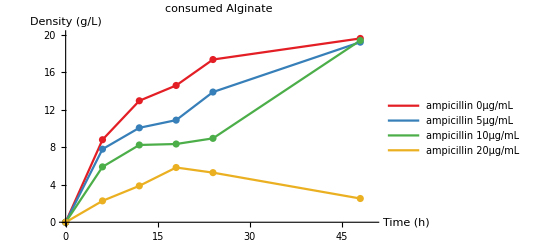

```mathematica
Show[ListPlot[{CSAlginatedata,CSAlginatedata05,CSAlginatedata10,CSAlginatedata20},PlotRange->{{0,50},{0,20}},Joined->True,PlotLegends->{"ampicillin 0μg/mL","ampicillin 5μg/mL","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["consumed Alginate",Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{CSAlginatedata,CSAlginatedata05,CSAlginatedata10,CSAlginatedata20},PlotRange->{{0,50},{0,20}},Joined->False,PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```

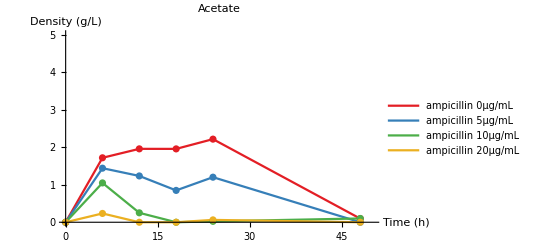

```mathematica
Show[ListPlot[{Acetatedata,Acetatedata05,Acetatedata10,Acetatedata20},PlotRange->{{0,50},{0,5}},Joined->True,PlotLegends->{"ampicillin 0μg/mL","ampicillin 5μg/mL","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["Acetate",Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{Acetatedata,Acetatedata05,Acetatedata10,Acetatedata20},PlotRange->{{0,50},{0,20}},Joined->False,PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```

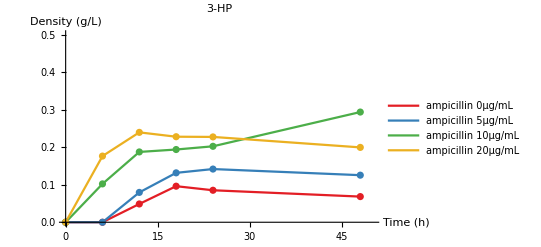

```mathematica
Show[ListPlot[{HPdata,HPdata05,HPdata10,HPdata20},PlotRange->{{0,50},{0,0.5}},Joined->True,PlotLegends->{"ampicillin 0μg/mL","ampicillin 5μg/mL","ampicillin 10μg/mL","ampicillin 20μg/mL"},PlotLabel->Style["3-HP",Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{HPdata,HPdata05,HPdata10,HPdata20},PlotRange->{{0,50},{0,20}},Joined->False,PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```

## Consumed alginate

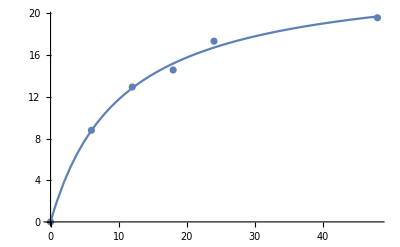

```mathematica
Show[Plot[(1.2005472384860392t)/(0.5214803449957723+0.0500520543762184t),{t,0,48}],ListPlot[CSAlginatedata]]
```

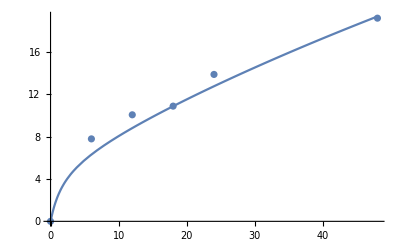

```mathematica
Show[Plot[(-1.2675830537363433+81.38182800702654t+4.626692481412568 t^2)/(24.21153321877431+12.961578563485084t+0.04618092931879026 t^2),{t,0,48}],ListPlot[CSAlginatedata05]]
```

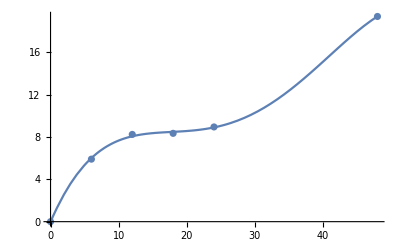

```mathematica
Show[Plot[-0.02195177+1.491836*t-0.09607548*t^2+0.002587028*t^3-0.00002203381*t^4,{t,0,48}],ListPlot[CSAlginatedata10]]
```

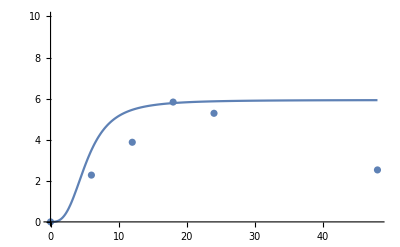

```mathematica
Show[Plot[(30.387212772255726 t^3)/(775.2742776345192+5.121312090538894 t^3),{t,0,48},PlotRange->{0,10}],ListPlot[CSAlginatedata20]]
```

```mathematica
CSAl0[t_]:=(1.2005472384860392t)/(0.5214803449957723+0.0500520543762184t)
CSAl05[t_]:=(-1.2675830537363433+81.38182800702654t+4.626692481412568 t^2)/(24.21153321877431+12.961578563485084t+0.04618092931879026 t^2)
CSAl10[t_]:=-0.02195177+1.491836*t-0.09607548*t^2+0.002587028*t^3-0.00002203381*t^4
CSAl20[t_]:=(30.387212772255726 t^3)/(775.2742776345192+5.121312090538894 t^3)
```

## Acetate

```mathematica
(*smooth step function using sigmoid*)
```

```mathematica
Ace=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter[t]-c Ac[t]/(d+Ac[t])Vibinter[t] 1/(1+Exp[-1(t-24)])+0.2CSAl0'[t],Ac[0]==0},Ac,{t,0,48},{a,K,c,d}];
Ace05=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter05[t]-c Ac[t]/(d+Ac[t])Vibinter05[t] 1/(1+Exp[-1(t-44)])+0.2CSAl05'[t],Ac[0]==0},Ac,{t,0,48},{a,K,c,d}];
Ace10=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter10[t]+0.2CSAl10'[t],Ac[0]==0},Ac,{t,0,48},{a,K}];
Ace20=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter20[t]+0.2CSAl20'[t],Ac[0]==0},Ac,{t,0,48},{a,K}];
```

```mathematica
AceEconly=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter[t]+0.2CSAl0'[t],Ac[0]==0},Ac,{t,0,48},{a,K}];
Ace05Econly=ParametricNDSolveValue[{Ac'[t]==-a Ac[t]/(K+Ac[t])Ecoliinter05[t]+0.2CSAl05'[t],Ac[0]==0},Ac,{t,0,48},{a,K}];
```

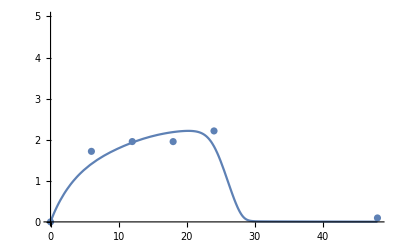

```mathematica
Show[Plot[Ace[0.04,0.30513230161658544,0.05,0.30513230161658544][t],{t,0,48},PlotRange->{0,5}],ListPlot[Acetatedata]]
```

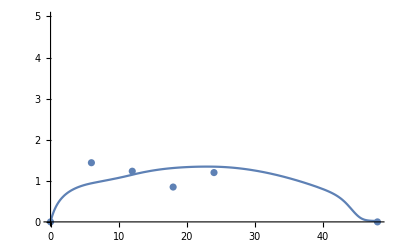

```mathematica
Show[Plot[Ace05[0.04,0.30513230161658544,0.05,0.30513230161658544][t],{t,0,48},PlotRange->{0,5}],ListPlot[Acetatedata05]]
```

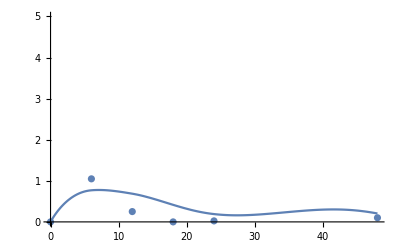

```mathematica
Show[Plot[Ace10[0.049,0.30513230161658544][t],{t,0,48},PlotRange->{0,5}],ListPlot[Acetatedata10]]
```

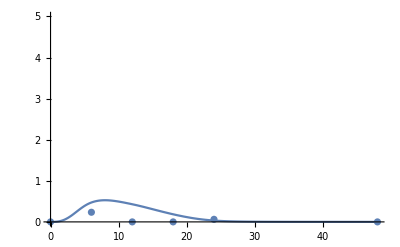

```mathematica
Show[Plot[Ace20[0.049,0.30513230161658544][t],{t,0,48},PlotRange->{0,5}],ListPlot[Acetatedata20]]
```

```mathematica
VcAce=ParametricNDSolveValue[{Ac'[t]==a(Ace[0.045,0.30513230161658544,0.05,0.30513230161658544][t])/(K+Ace[0.045,0.30513230161658544,0.05,0.30513230161658544][t])Vibinter[t],Ac[24]==0},Ac,{t,24,48},{a,K}];
```

```mathematica
VcAce05=ParametricNDSolveValue[{Ac'[t]==a(Ace05[0.045,0.30513230161658544,0.05,0.30513230161658544][t])/(K+Ace05[0.045,0.30513230161658544,0.05,0.30513230161658544][t])Vibinter[t],Ac[44]==0},Ac,{t,44,48},{a,K}];
```

## Ecoli

```mathematica
EcoliM0=ParametricNDSolveValue[{EM'[t]==a(0.2CSAl0'[t]-AceEconly[0.045,0.30513230161658544]'[t])-kd EM[t],EM[0]==Ecoliinter[0]},EM,{t,0,48},{a,kd}];
```

```mathematica
EcoliM05=ParametricNDSolveValue[{EM'[t]==a(0.2CSAl05'[t]-Ace05Econly[0.045,0.30513230161658544]'[t])-kd EM[t],EM[0]==Ecoliinter[0]},EM,{t,0,48},{a,kd}];
```

```mathematica
EcoliM10=ParametricNDSolveValue[{EM'[t]==a(0.2CSAl10'[t]-Ace10[0.045,0.30513230161658544]'[t])-kd EM[t],EM[0]==Ecoliinter[0]},EM,{t,0,48},{a,kd}];
```

```mathematica
EcoliM20=ParametricNDSolveValue[{EM'[t]==a(0.2CSAl20'[t]-Ace20[0.045,0.30513230161658544]'[t])-kd EM[t],EM[0]==Ecoliinter[0]},EM,{t,0,48},{a,kd}];
```

## 3-HP

```mathematica
HP30[t_]:=0.07(0.2CSAl0[t]-AceEconly[0.04,0.30513230161658544][t])
HP305[t_]:=0.07(0.2CSAl05[t]-Ace05Econly[0.04,0.30513230161658544][t])
HP310[t_]:=0.07(0.2CSAl10[t]-Ace10[0.049,0.30513230161658544][t])
HP320[t_]:=0.07(0.2CSAl20[t]-Ace20[0.049,0.30513230161658544][t])
```

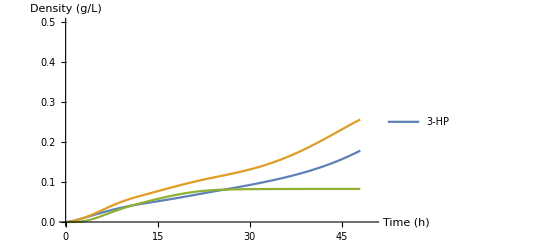

```mathematica
Plot[{HP30[t],HP310[t],HP320[t]},{t,0,48},PlotRange->{{0,50},{0,0.5}},PlotLegends->{"3-HP"},AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold]]
```

## Vibrio

```mathematica
Amp05=ParametricNDSolveValue[{Amp'[t]==-ka Amp[t]/(Amp[t]+Ka)HP305[t],Amp[0]==20},Amp,{t,0,48},{ka,Ka}];
Amp10=ParametricNDSolveValue[{Amp'[t]==-ka Amp[t]/(Amp[t]+Ka)HP310[t],Amp[0]==20},Amp,{t,0,48},{ka,Ka}];
Amp20=ParametricNDSolveValue[{Amp'[t]==-ka Amp[t]/(Amp[t]+Ka)HP320[t],Amp[0]==20},Amp,{t,0,48},{ka,Ka}];
```

```mathematica
VibrioP0=ParametricNDSolveValue[{VM'[t]==a*CSAl0'[t]+b*VcAce[0.02,0.305]'[t]HeavisideTheta[t-24]-kd VM[t],VM[0]==Vibinter[0]},VM,{t,0,48},{a,b,kd}];
```

```mathematica
VibrioP05=ParametricNDSolveValue[{VM'[t]==a*CSAl05'[t]+b*VcAce05[0.02,0.305]'[t]HeavisideTheta[t-44]-kd VM[t]-0.1(Amp05[4,5][t])/(5+Amp05[4,5][t]),VM[0]==Vibinter[0]},VM,{t,0,48},{a,b,kd}];
```

```mathematica
VibrioP10=ParametricNDSolveValue[{VM'[t]==a*CSAl10'[t]-kd VM[t]-0.1(Amp10[4,5][t])/(5+Amp10[4,5][t]),VM[0]==Vibinter[0]},VM,{t,0,48},{a,b,kd}];
```

```mathematica
VibrioP20=ParametricNDSolveValue[{VM'[t]==a*CSAl20'[t]-kd VM[t]-0.1(Amp20[4,5][t])/(5+Amp20[4,5][t]),VM[0]==Vibinter[0]},VM,{t,0,48},{a,b,kd}];
```

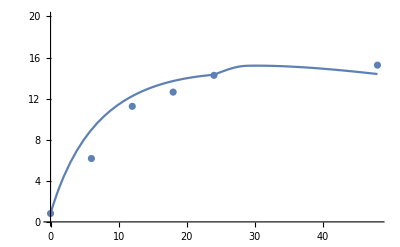

```mathematica
Show[Plot[VibrioP0[0.97,0.90,0.0104][t],{t,0,48},PlotRange->{0,20}],ListPlot[Vibriodata]]
```

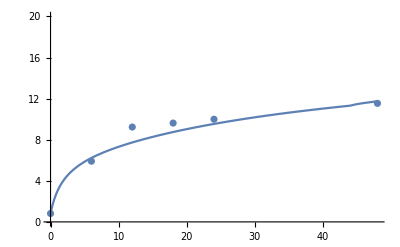

```mathematica
Show[Plot[VibrioP05[0.97,0.90,0.0104][t],{t,0,48},PlotRange->{0,20}],ListPlot[Vibriodata05]]
```

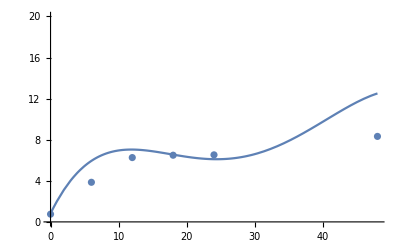

```mathematica
Show[Plot[VibrioP10[0.97,0.90,0.0104][t],{t,0,48},PlotRange->{0,20}],ListPlot[Vibriodata10]]
```

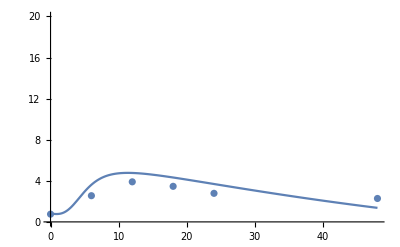

```mathematica
Show[Plot[VibrioP20[0.97,0.90,0.0104][t],{t,0,48},PlotRange->{0,20}],ListPlot[Vibriodata20]]
```

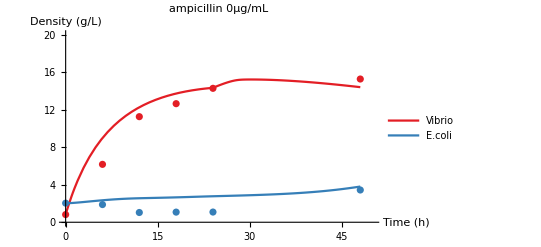

```mathematica
Show[Plot[{VibrioP0[0.97,0.90,0.0104][t],EcoliM0[1.24,0.013][t]},{t,0,48},PlotRange->{{0,50},{0,20}},PlotLegends->{"Vibrio","E.coli"},PlotLabel->Style["ampicillin 0μg/mL",Italic,Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{Vibriodata,Ecolidata},PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```

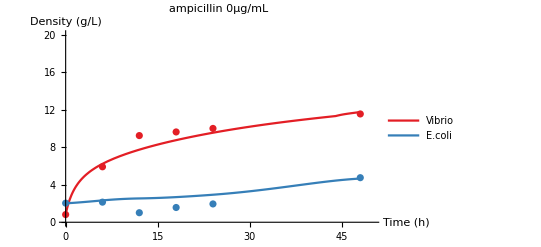

```mathematica
Show[Plot[{VibrioP05[0.97,0.90,0.0104][t],EcoliM05[1.24,0.013][t]},{t,0,48},PlotRange->{{0,50},{0,20}},PlotLegends->{"Vibrio","E.coli"},PlotLabel->Style["ampicillin 0μg/mL",Italic,Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{Vibriodata05,Ecolidata05},PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```

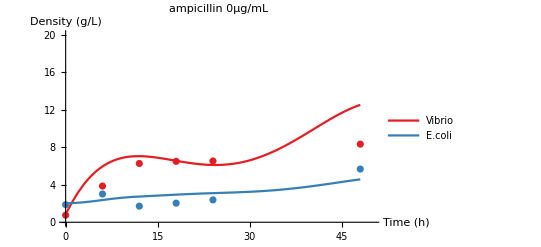

```mathematica
Show[Plot[{VibrioP10[0.97,0.90,0.0104][t],EcoliM10[1.24,0.013][t]},{t,0,48},PlotRange->{{0,50},{0,20}},PlotLegends->{"Vibrio","E.coli"},PlotLabel->Style["ampicillin 0μg/mL",Italic,Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{Vibriodata10,Ecolidata10},PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```

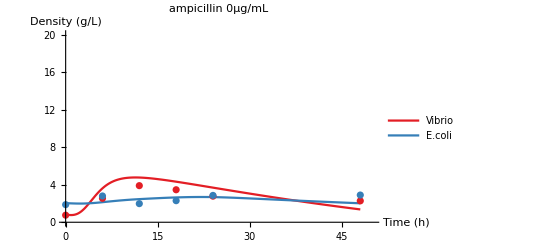

```mathematica
Show[Plot[{VibrioP20[0.97,0.90,0.0104][t],EcoliM20[1.24,0.013][t]},{t,0,48},PlotRange->{{0,50},{0,20}},PlotLegends->{"Vibrio","E.coli"},PlotLabel->Style["ampicillin 0μg/mL",Italic,Bold],AxesLabel->{"Time (h)","Density (g/L)"},LabelStyle->Directive[Larger,Bold],PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}],ListPlot[{Vibriodata20,Ecolidata20},PlotStyle->{RGBColor[228/256,30/256,37/256],RGBColor[54/256,127/256,185/256],RGBColor[76/256,175/256,73/256],RGBColor[236/256,177/256,33/256]}]]
```